```mathematica
k0= 100
```

100

```mathematica
dk=1/2
```

1/2

```mathematica
k1=k0-dk/2
```

399/4

```mathematica
k2=k0
```

100

```mathematica
k3=k0+dk/2
```

401/4

```mathematica
ψ[x_]:=Piecewise[{{Exp[I k1 x],x<0},{Exp[I k2 x],x==0},{Exp[I k3 x],x>0}}]
```

```mathematica
conjug[x_]:=Conjugate[ψ[x]]* ψ[x]
```

```mathematica
normConst=Integrate[conjug[x],{x,-Pi,Pi}]
```

2 π

```mathematica
N=1/Sqrt[normConst]
```

Set::wrsym: Symbol N is Protected.

1/(√(2 π))

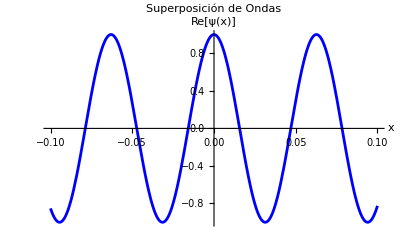

```mathematica
Plot[Re[ψ[x]],{x,-0.1,0.1},PlotLabel->"Superposición de Ondas",AxesLabel->{"x","Re[ψ(x)]"},PlotStyle->Blue]
```

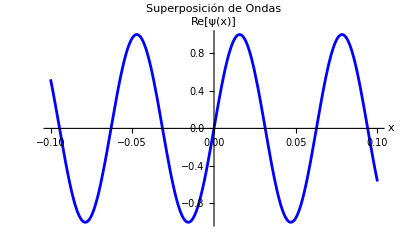

```mathematica
Plot[Im[ψ[x]],{x,-0.1,0.1},PlotLabel->"Superposición de Ondas",AxesLabel->{"x","Re[ψ(x)]"},PlotStyle->Blue]
```

```mathematica
pOp[x_]:=-I D[ψ[x],x]
```

```mathematica
pMedia=Integrate[Conjugate[ψ[x]]pOp[x],{x,-Pi,Pi}]
```

200 π

```mathematica
pVarianza=Integrate[Conjugate[ψ[x]] (pOp[x]-pMedia)^2 ψ[x],{x,-Pi,Pi}]
```

(1/4-ⅈ/4) (ⅈ+(160000+160000 ⅈ) π^3)

```mathematica
pStdDev=Sqrt[pVarianza]
```

1/2 √((1-ⅈ) (ⅈ+(160000+160000 ⅈ) π^3))

```mathematica
xMedia=NIntegrate[x Abs[ψ[x]]^2,{x,-Pi,Pi}]
```

0.

```mathematica
x2Media=NIntegrate[x^2 Abs[ψ[x]]^2,{x,-Pi,Pi}]
```

20.6709

```mathematica
xVar=x2Media-xMedia^2
```

20.6709

```mathematica
incertidumbre=xVar*pVar
```

5.12741×10^7+5.16771 ⅈ

```mathematica
ℏ=1.054571817*10^-34
```

1.05457×10^-34

```mathematica
verificacion=incertidumbre>=ℏ/2
```

GreaterEqual::nord: Invalid comparison with 5.12741×10^7+5.16771 ⅈ attempted.

```mathematica
5.127409549172908*^7+5.167712777853012 ⅈ≥5.272859085000001*^-35
```

GreaterEqual::nord: Invalid comparison with 5.12741×10^7+5.16771 ⅈ attempted.

5.12741×10^7+5.16771 ⅈ≥5.27286×10^-35

```mathematica
deltaX=Sqrt[xVar]
```

4.54652